## Set Directory

```mathematica
SetDirectory[NotebookDirectory[]];
```

Position extractor by names

```mathematica
ExtractorByNames[labels_,varlabels_]:=Block[{notfoundQ,xpos,ypos},
notfoundQ=Flatten[Position[labels,varlabels[[1]]]]=={};
If[notfoundQ,
Print["Not able to find the provided label = ",varlabels[[1]] ;]
,
xpos= Flatten[Position[labels,varlabels[[1]]]][[1]];
];
notfoundQ=Flatten[Position[labels,varlabels[[2]]]]=={};
If[notfoundQ,
Print["Not able to find the provided label = ",varlabels[[1]] ;]
,
ypos= Flatten[Position[labels,varlabels[[2]]]][[1]];
];
Return[{xpos,ypos}];
];
```

Loading RK raw data

```mathematica
rkrawdata=Import["ElastoPlasticRKdata.txt","Data"];
rklabels=rkrawdata[[1]];
rkdata = Drop[rkrawdata,1];
```

```mathematica
rklabels
```

{radius,u,sigma_rr,sigma_tt,sigma_zz,eps_rr,eps_tt,eps_zz,eps_p_rr,eps_p_tt,eps_p_zz}

Loading Paraview data

```mathematica
(*pvrawdata=Import["ElastoPlasticFEMdata.csv","Data"]; *)
(*pvrawdata=Import["ElastoPlasticIntPoints-CPU.csv","Data"];*)
pvrawdata=Import["ElastoPlasticIntPoints.csv","Data"];
pvlabels=pvrawdata[[1]]
pvdata = Drop[pvrawdata,1];
```

{Displacement:0,Displacement:1,Displacement:2,FailureType,Strain:0,Strain:1,Strain:2,Strain:3,Strain:4,Strain:5,Strain:6,Strain:7,Strain:8,StrainPlastic:0,StrainPlastic:1,StrainPlastic:2,StrainPlastic:3,StrainPlastic:4,StrainPlastic:5,StrainPlastic:6,StrainPlastic:7,StrainPlastic:8,Stress:0,Stress:1,Stress:2,Stress:3,Stress:4,Stress:5,Stress:6,Stress:7,Stress:8,vtkValidPointMask,arc_length,Points:0,Points:1,Points:2}

Applying radius shift because plot over line start on rw (?_?)

```mathematica
rw=0.1;
rpos=ExtractorByNames[pvlabels,{"arc_length","arc_length"}][[1]];
pvdata[[All,{rpos}]]+=rw;
```

```mathematica
pvlabels
```

{Displacement:0,Displacement:1,Displacement:2,FailureType,Strain:0,Strain:1,Strain:2,Strain:3,Strain:4,Strain:5,Strain:6,Strain:7,Strain:8,StrainPlastic:0,StrainPlastic:1,StrainPlastic:2,StrainPlastic:3,StrainPlastic:4,StrainPlastic:5,StrainPlastic:6,StrainPlastic:7,StrainPlastic:8,Stress:0,Stress:1,Stress:2,Stress:3,Stress:4,Stress:5,Stress:6,Stress:7,Stress:8,vtkValidPointMask,arc_length,Points:0,Points:1,Points:2}

## Plots controls

```mathematica
colors=ColorData[81,"ColorList"];
```

```mathematica
fonts = 16;
rkrules={PlotRange->All,Frame->True,FrameStyle->Directive[Black,fonts], GridLines->Automatic,PlotStyle->colors[[2]],Joined->True, ImageSize->500,PlotLegends-> {"Runge-Kutta Method"}};
pvrules={PlotRange->All,Frame->True,FrameStyle->Directive[Black,fonts],PlotMarkers->Automatic, GridLines->Automatic,PlotStyle->colors[[1]],Joined->True, ImageSize->500,PlotLegends-> {"FEM"}};
```

Rendering RK plots

```mathematica
grku=ListPlot[rkdata[[All,ExtractorByNames[rklabels,{"radius","u"}]]],rkrules, FrameLabel->{Style["radius",Black,Bold,fonts],Style["u",Black,Bold,fonts]}];
grksigmar=ListPlot[rkdata[[All,ExtractorByNames[rklabels,{"radius","sigma_rr"}]]],rkrules, FrameLabel->{Style["radius",Black,Bold,fonts],Style["Δsigma_rr",Black,Bold,fonts]}];
grksigmat=ListPlot[rkdata[[All,ExtractorByNames[rklabels,{"radius","sigma_tt"}]]],rkrules, FrameLabel->{Style["radius",Black,Bold,fonts],Style["Δsigma_θθ",Black,Bold,fonts]}];
grkepsr=ListPlot[rkdata[[All,ExtractorByNames[rklabels,{"radius","eps_rr"}]]],rkrules, FrameLabel->{Style["radius",Black,Bold,fonts],Style["Δeps_rr",Black,Bold,fonts]}];
grkepst=ListPlot[rkdata[[All,ExtractorByNames[rklabels,{"radius","eps_tt"}]]],rkrules, FrameLabel->{Style["radius",Black,Bold,fonts],Style["Δeps_θθ",Black,Bold,fonts]}];
grkepspr=ListPlot[rkdata[[All,ExtractorByNames[rklabels,{"radius","eps_p_rr"}]]],rkrules, FrameLabel->{Style["radius",Black,Bold,fonts],Style["Δepsp_rr",Black,Bold,fonts]}];
grkepspt=ListPlot[rkdata[[All,ExtractorByNames[rklabels,{"radius","eps_p_tt"}]]],rkrules, FrameLabel->{Style["radius",Black,Bold,fonts],Style["Δepsp_θθ",Black,Bold,fonts]}];
```

Rendering Paraview plots

```mathematica
gpvu=ListPlot[pvdata[[All,ExtractorByNames[pvlabels,{"arc_length","Displacement:0"}]]],pvrules, FrameLabel->{Style["radius",Black,Bold,fonts],Style["u",Black,Bold,fonts]}];
gpvsigmar=ListPlot[pvdata[[All,ExtractorByNames[pvlabels,{"arc_length","Stress:0"}]]],pvrules, FrameLabel->{Style["radius",Black,Bold,fonts],Style["Δsigma_rr",Black,Bold,fonts]}];
gpvsigmat=ListPlot[pvdata[[All,ExtractorByNames[pvlabels,{"arc_length","Stress:4"}]]],pvrules, FrameLabel->{Style["radius",Black,Bold,fonts],Style["Δsigma_θθ",Black,Bold,fonts]}];
gpvepsr=ListPlot[pvdata[[All,ExtractorByNames[pvlabels,{"arc_length","Strain:0"}]]],pvrules, FrameLabel->{Style["radius",Black,Bold,fonts],Style["Δeps_rr",Black,Bold,fonts]}];
gpvepst=ListPlot[pvdata[[All,ExtractorByNames[pvlabels,{"arc_length","Strain:4"}]]],pvrules, FrameLabel->{Style["radius",Black,Bold,fonts],Style["Δeps_θθ",Black,Bold,fonts]}];
gpvepspr=ListPlot[pvdata[[All,ExtractorByNames[pvlabels,{"arc_length","StrainPlastic:0"}]]],pvrules, FrameLabel->{Style["radius",Black,Bold,fonts],Style["Δepsp_rr",Black,Bold,fonts]}];
gpvepspt=ListPlot[pvdata[[All,ExtractorByNames[pvlabels,{"arc_length","StrainPlastic:4"}]]],pvrules, FrameLabel->{Style["radius",Black,Bold,fonts],Style["Δepsp_θθ",Black,Bold,fonts]}];
```

## Comparison plots

```mathematica
gcompu=Show[{gpvu,grku}];
gcompsigmar=Show[{gpvsigmar,grksigmar},PlotRange->All];
gcompsigmat=Show[{gpvsigmat,grksigmat},PlotRange->All];
gcompepsr=Show[{gpvepsr,grkepsr},PlotRange->All];
gcompepst=Show[{gpvepst,grkepst},PlotRange->All];
gcompepspr=Show[{gpvepspr,grkepspr},PlotRange->All];
gcompepspt=Show[{gpvepspt,grkepspt},PlotRange->All];
```

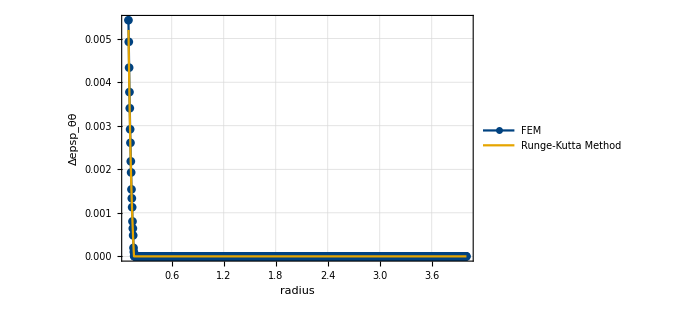

```mathematica
gcompepspt
```

## Exporting plots

```mathematica
imageres=200;
RedenderplotsQ=True;
If[RedenderplotsQ,
Export["elastoplastic_comp_u.png",gcompu,ImageResolution-> imageres];
Export["elastoplastic_comp_sigma_r.png",gcompsigmar,ImageResolution-> imageres];
Export["elastoplastic_comp_sigma_t.png",gcompsigmat,ImageResolution-> imageres];
Export["elastoplastic_comp_eps_r.png",gcompepsr,ImageResolution-> imageres];
Export["elastoplastic_comp_eps_t.png",gcompepst,ImageResolution-> imageres];
Export["elastoplastic_comp_eps_p_r.png",gcompepspr,ImageResolution-> imageres];
Export["elastoplastic_comp_eps_p_t.png",gcompepspt,ImageResolution-> imageres];
];
```

## BC data for RK approximation

```mathematica
Print["ur and σr at Re = ",pvdata[[All,ExtractorByNames[pvlabels,{"Displacement:0","Stress:0"}]]][[-1]]]
```

ur and σr at Re = {0,-0.00023706}